```mathematica
c={Red,Green,Blue,Cyan,Magenta,Yellow,Purple,Orange,Black}
ColorNegate[c]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 1],RGBColor[1, 0, 1],RGBColor[1, 1, 0],RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0],GrayLevel[0]}

{RGBColor[0., 1., 1.],RGBColor[1., 0., 1.],RGBColor[1., 1., 0.],RGBColor[1., 0., 0.],RGBColor[0., 1., 0.],RGBColor[0., 0., 1.],RGBColor[0.5, 1., 0.5],RGBColor[0., 0.5, 1.],GrayLevel[1.]}

If you negate the “display (emitted light) primaries” red, green, blue, you get the “print (reflected light) primaries” cyan, magenta, yellow.

```mathematica
Blend/@{{Red,Cyan},{Green,Magenta},{Blue,Yellow}}
```

{RGBColor[Rational[1, 2], Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], Rational[1, 2]]}

```mathematica
Blend[{Yellow,Pink,Green}]
```

RGBColor[Rational[2, 3], 0.8333333333333333, 0.16666666666666666]

```mathematica
Table[RGBColor[0,g,1],{g,0,1,0.05}]
```

{RGBColor[0, 0., 1],RGBColor[0, 0.05, 1],RGBColor[0, 0.1, 1],RGBColor[0, 0.15000000000000002, 1],RGBColor[0, 0.2, 1],RGBColor[0, 0.25, 1],RGBColor[0, 0.30000000000000004, 1],RGBColor[0, 0.35000000000000003, 1],RGBColor[0, 0.4, 1],RGBColor[0, 0.45, 1],RGBColor[0, 0.5, 1],RGBColor[0, 0.55, 1],RGBColor[0, 0.6000000000000001, 1],RGBColor[0, 0.65, 1],RGBColor[0, 0.7000000000000001, 1],RGBColor[0, 0.75, 1],RGBColor[0, 0.8, 1],RGBColor[0, 0.8500000000000001, 1],RGBColor[0, 0.9, 1],RGBColor[0, 0.9500000000000001, 1],RGBColor[0, 1., 1]}

```mathematica
Table[Hue[x],{x,0,1,0.05}]
```

{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]}

```mathematica
Table[Style[RandomInteger[1000],RandomColor[]],14]
```

{147,124,825,292,449,866,757,39,720,189,856,901,775,321}

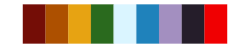

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}

```mathematica
ColorData[16,"Panel"]
ColorData[3,"ColorList"]
```

```mathematica
Graphics3D[{RGBColor[0,1,0,.5],Cone[]}]
```

-Graphics3D-

```mathematica
{RGBColor["#00ff00"],RGBColor["maroon"]}
```

{RGBColor[0., 1., 0.],RGBColor[0.5019607843137255, 0., 0.]}

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],Hue[h]]],{n,5,20,1},{h,0,1}]
```